```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
eq[x_,μ_]=μ x (1-x)
```

(1-x) x μ

```mathematica
eq3[x_,μ_]=FullSimplify[eq[eq[eq[x,μ],μ],μ]]
```

(1-x) x μ^3 (1+(-1+x) x μ) (1+(-1+x) x μ^2 (1+(-1+x) x μ))

```mathematica
s=Solve[eq3[x,μ]==x,x]
```

{{x→0},{x→(-1+μ)/μ},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,1]},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,2]},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,3]},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,4]},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,5]},{x→Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,6]}}

```mathematica
LIS=s⟦2;;,1,2⟧
```

{(-1+μ)/μ,Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,1],Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,2],Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,3],Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,4],Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,5],Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,6]}

```mathematica
Block[{μ=4},N[D[eq3[x,μ],{x}]/.s⟦2;;⟧]]
```

{-8.,-8.,8.,-8.,8.,8.,-8.}

```mathematica
LIS/. μ-> 3.
```

{0.666667,0.199258-0.137831 ⅈ,0.199258+0.137831 ⅈ,0.535655-0.248708 ⅈ,0.535655+0.248708 ⅈ,0.931754-0.0532057 ⅈ,0.931754+0.0532057 ⅈ}

```mathematica
LIS⟦2⟧/. μ-> 4.
```

0.116978

```mathematica
Collect[Series[eq3[z,μ],{z,LIS⟦2⟧,2}]/. μ-> 3.,z]
```

(3.92909+1.63882 ⅈ)-(21.9783+23.5769 ⅈ) z+(25.153+61.5046 ⅈ) z^2

```mathematica
Collect[Series[eq3[z,μ],{z,LIS⟦3⟧,2}]/. μ-> 3.,z]
```

(3.92909-1.63882 ⅈ)-(21.9783-23.5769 ⅈ) z+(25.153-61.5046 ⅈ) z^2

```mathematica
f[μ_]=Collect[Series[eq3[z,μ],{z,LIS⟦2⟧,2}],z]+Collect[Series[eq3[z,μ],{z,LIS⟦3⟧,2}],z];
```

```mathematica
Chop[f[3.],10^-3]
```

7.85817-43.9566 z+50.3061 z^2

```mathematica
Table[{μ,f[μ]},{μ,3.,4.,0.9}]
```

{{3.,(7.85817+0. ⅈ)-(43.9566+0. ⅈ) z+(50.3061+0. ⅈ) z^2},{3.9,4.16747-54.2475 z+184.265 z^2}}

```mathematica
Plot3D[Chop[f[1. μ],10^-3],{μ,3,4},{z,0,1}]
```

-Graphics3D-

```mathematica
Plot[D1R,{μ,3.5,4},Frame->True,PlotRange->All,PlotStyle->{Dotted,Dashed}]
```

-Graphics-

```mathematica
Plot[D1R,{μ,3.5,4},Frame->True,PlotRange->{-10,10},PlotStyle->{Dotted,Dashed},GridLines->Automatic]
```

-Graphics-

```mathematica
Plot[D1I,{μ,3.5,4},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
Plot[D1,{μ,3.5,4},Frame->True,PlotRange->All,PlotStyle->{Dotted,Dashed}]
```

-Graphics-

```mathematica
Plot[D1,{μ,3.8,3.85},Frame->True,PlotRange->{0,10},PlotStyle->{{Red,Dotted},{Blue,Dashed},{Green,Dotted},{Orange,Dashed},{Black,Dotted},{Magenta,Dashed},{Brown,Dotted}}]
```

-Graphics-

```mathematica
D2=Abs[FullSimplify[D[eq3[x,μ],{x,2}]]]/.s⟦2;;⟧;
```

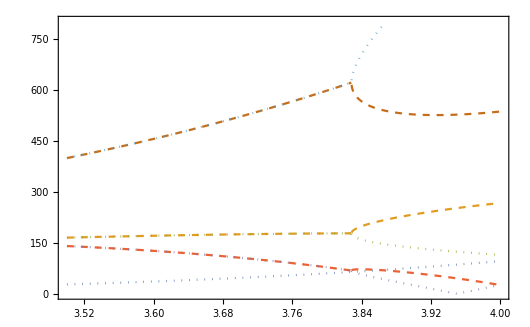

```mathematica
Plot[D2,{μ,3.5,4},Frame->True,PlotStyle->{Dotted,Dashed},PlotRange->{0,800}]
```

```mathematica
fav[μ_]:=Chop[Total[LIS⟦2;;⟧]/3,10^-6]
```

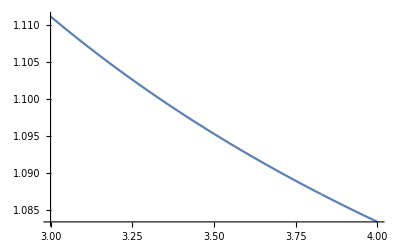

```mathematica
Plot[Re[fav[μ]],{μ,3,4}]
```

```mathematica
Length[LIS]
```

7

```mathematica
Length[D2]
```

7

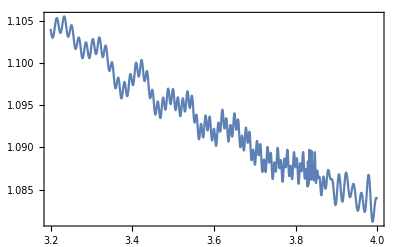

```mathematica
ans[μ_]=fav[μ]-10^-3(Cos[D2⟦2⟧]+Cos[D2⟦4⟧]+Cos[D2⟦6⟧]);
Plot[ans[μ],{μ,3.2,4},Frame->True]
```

```mathematica
D2⟦1⟧/. μ-> 3.5
```

27.5625

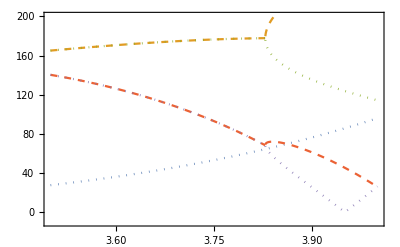

```mathematica
Plot[D2,{μ,3.5,4},Frame->True,PlotStyle->{Dotted,Dashed},PlotRange->{-10,200}]
```

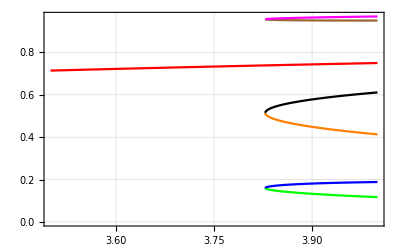

```mathematica
Plot[LIS,{μ,3.5,4},GridLines->Automatic,PlotStyle->{Red,Green,Blue,Orange,Black,Brown,Magenta},Frame->True]
```

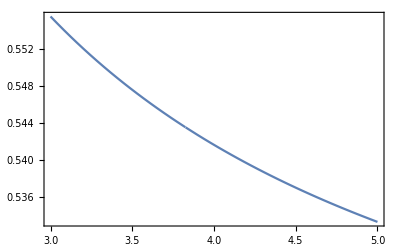

```mathematica
Plot[Mean[LIS⟦2;;⟧],{μ,3,5},Frame->True]
```

```mathematica
FullSimplify[Total[LIS⟦2;;⟧]]
```

3+1/μ

```mathematica
FullSimplify[LIS⟦3⟧+LIS⟦5⟧+LIS⟦6⟧]
```

Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,2]+Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,4]+Root[1+μ+μ^2+(-μ-2 μ^2-2 μ^3-μ^4) #1+(μ^2+3 μ^3+3 μ^4+2 μ^5) #1^2+(-μ^3-3 μ^4-5 μ^5-μ^6) #1^3+(μ^4+4 μ^5+3 μ^6) #1^4+(-μ^5-3 μ^6) #1^5+μ^6 #1^6&,5]

```mathematica
LIS/. μ-> 4.
```

{0.75,0.116978,0.188255,0.413176,0.61126,0.950484,0.969846}

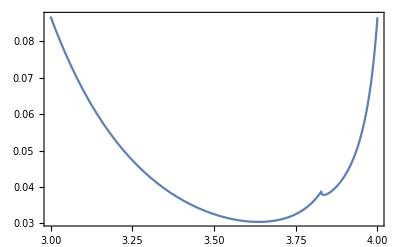

```mathematica
Plot[(1/Abs[D[eq3[x,μ],{x,2}]/.s⟦2⟧](LIS⟦2⟧+LIS⟦3⟧)+1/Abs[D[eq3[x,μ],{x,2}]/.s⟦4⟧](LIS⟦4⟧+LIS⟦5⟧)+1/Abs[D[eq3[x,μ],{x,2}]/.s⟦5⟧](LIS⟦6⟧+LIS⟦7⟧)),{μ,3,4},Frame->True]
```

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦1⟧/. μ-> 3.4
```

-1254.58

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦2⟧/. μ-> 3.
```

-6.

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦3⟧/. μ-> 3.
```

50.3061+123.009 ⅈ

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦4⟧/. μ-> 3.01
```

51.9704-122.938 ⅈ

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦5⟧/. μ-> 3.
```

127.058+81.0065 ⅈ

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦6⟧/. μ-> 3.01
```

127.877-80.4216 ⅈ

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦7⟧/. μ-> 3.
```

-39.3644+216.016 ⅈ

```mathematica
D[eq3[x,μ],{x,2}]/.s⟦8⟧/. μ-> 3.01
```

-42.8653-217.741 ⅈ

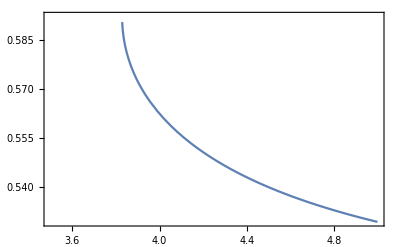

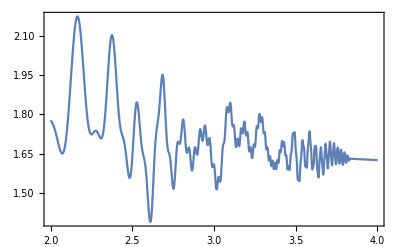

```mathematica
Plot[Mean[{LIS⟦1⟧,LIS⟦2⟧,LIS⟦4⟧,LIS⟦7⟧}],{μ,3.5,5},Frame->True]
```